```mathematica
TOP MASS EXTRACTION;
```

```mathematica
PSEUDO DATA GENERATOR;
```

IMPORTANT VARIABLES;

```mathematica
(*mt=173.2 GeV and Scale =173,2, invarian mass of tt bar*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
Needs["HypothesisTesting`"]
mass={168.2, 170.7,173.2,175.7,178.2};
nmass=Length[mass];
number=3;
pvaluestandard=0.0455;
```

C:\Users\Lalu Zam\Documents\top-quark-thesis\mathematica

```mathematica
DATA FROM HELAC (FOR STANDARD PSEUDODATA GENERATOR);
```

```mathematica
file=Table[FileNames[][[i+5]],{i,1,nmass}];
nbins=20;

start[n_]:=2+(n-1)*20
data=Block[{list},
list=Reap[Do[Sow[ReadList[file[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahist[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[data[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossection=Table[Reap[Do[Sow[data[[j,1]]],{j,1,nmass,1}]][[2,1,j,2]],{j,1,nmass}] (*fb*)
```

{951.072,930.023,906.377,882.921,859.732}

```mathematica
INPUT;
```

```mathematica
luminosity=35(*fb^-1*);
numbevents=Table[crossection[[i]]*luminosity*4,{i,1,Length[crossection]}];
stdnevents =Round[IntegerPart[numbevents[[number]]]/4]
numbofdiffdist=7;
nevents=130000;
int=2;
rebin=5;
npseudobin=5;
fitf={x};
npseudo=100
```

31723

100

```mathematica
NAMING SCHEME;
```

```mathematica
variable={"M_(t OverscriptBox[t, _])","p_(T, t) average", "p_(T, b OverscriptBox[b, _])", "M_b_1 average" , "M_(e^+)","M_(e^+)","M_(e^+)","min(M_(e^+),M_(e^+))","p_(T, SubscriptBox[b, 1])","p_(T, SubscriptBox[b, 2])","p_(T, b) average", "p_(T, SuperscriptBox[e, +])",
"p_(T, SuperscriptBox[μ, -])","p_(T, l) average", "p_(T, SuperscriptBox[e, +] SuperscriptBox[μ, -])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 1])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 2])", "p_(T, miss)","y_t average", "y_b average", "y_(e^+)","y_(μ^-)", "y_l average","y_(t OverscriptBox[t, _])","y_(b OverscriptBox[b, _])","ΔR_b_1","ΔR_(e^+)","ΔR_(e^+)","ΔR_(e^+)","ΔR_(μ^-)","ΔR_(μ^-)","ΔR_(t OverscriptBox[t, _])","y_(e^+)","p_(T, SubscriptBox[l, 1])","p_(T, SubscriptBox[l, 2])","y_l_1","y_l_2"};varnorm=Table["1/σ"<>ToString[(("d "σ)/("d" variable[[i]])),StandardForm],{i,1,Length[variable]}];
varname={"Mttbar","PTt_ave", "PTbbar","Mb1b2_ave","Me+b1","Me+b2","Me+mu-","min(Me+b1_Me+b2)","PTb1","PTb2","PTb_ave","PTe+","PTmu-","PTl_ave","PTe+mu-","PTe+b1","PTe+b2","PT_miss","yt_ave","yb_ave","ye+","ymu-","yl_ave","yttbar","ybbar","kdeltaRb1b2","kdeltaRe+mu-","kdeltaRe+b1","kdeltaRe+b2","kdeltaRmu-b1","kdeltaRmu-b2","kdeltaRttbar","ye+mu-","PTl1","PTl2","yl1","yl2"};
scalename={"et2","mt"};
scale={"E_T/2","mt"};
lum={"5 fb^-1","35 fb^-1"};
massname={"168,2","170,7","173,2","175,7","178,2"};
```

```mathematica
DATA LIST ;
```

```mathematica
bins=Partition[Block[{bin},
bin=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidth=Table[(Max[bins[[i]]]-Min[bins[[i]]])/(nbins-1),{i,1,nmass}];
binsreal=Reap[Do[Sow[Chop[bins[[i]]-binwidth[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsreal[[i]],Max[binsreal[[i]]]+binwidth[[i]]]],{i,1,nmass,1}]][[2,1]];
bwreal=Table[(Max[binsreal[[i]]]-Min[binsreal[[i]]])/(nbins),{i,1,nmass}];
factor=Table[Sum[vals[[j,i]],{i,1,20,1}]*bwreal[[j]]*10^-3,{j,1,nmass}]; (*area under the histogram*)

vals=Partition[Block[{val},
val=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnorm=Table[vals[[i]]/(crossection[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)
valsnorm[[3]]

counts=Partition[Block[{count},
count=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,4]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
countsmax=Table[Sum[counts[[i,j]],{j,1,Length[counts[[i]]]}],{i,1,nmass}];
countsnorm=Table[counts[[i]]/countsmax[[i]],{i,1,nmass}];

error=Partition[Block[{err},
err=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnorm=Table[error[[i]]/(crossection[[i]]),{i,1,nmass}];
normalisation=Round[Table[Sum[valsnorm[[j,i]],{i,1,Length[valsnorm[[j]]]}]*binwidth[[j]],{j,1,nmass}]]

REBINNING;
valsrebin=Table[Table[Sum[Partition[vals[[k]],Round[nbins/rebin]][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
valsnormrebin=Table[Table[Sum[Partition[valsnorm[[k]],Round[nbins/rebin]][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
errnormrebin=Table[Table[Sum[Partition[errnorm[[k]],Round[nbins/rebin]][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
countsrebin=Table[Table[Sum[Partition[counts[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}],{j,1,rebin}],{k,1,nmass}];
countsnormrebin=N[Table[Table[Sum[Partition[countsnorm[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}],{j,1,rebin}],{k,1,nmass}]];

binsrebin=Table[Table[First[Partition[bins[[j]],(Round[nbins/rebin])][[i]]],{i,1,rebin}],{j,1,nmass}];
bwrebin=Table[(Max[binsrebin[[i]]]-Min[binsrebin[[i]]])/(rebin-1),{i,1,nmass}];
binsrebinreal=Reap[Do[Sow[Chop[binsrebin[[i]]-bwrebin[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrebinreal[[i]],Max[binsrebinreal[[i]]]+bwrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrebinreal=Table[(Max[binsrebinreal[[i]]]-Min[binsrebinreal[[i]]])/(rebin),{i,1,nmass}];
normalisationrebin=Round[Table[Sum[valsnormrebin[[j,i]],{i,1,Length[valsnormrebin[[j]]]}]*bwrebinreal[[j]],{j,1,nmass}]]
```

Part::partd: Part specification vals⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification vals⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification vals⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0.,0.000393051,0.00173728,0.00252026,0.00324339,0.00408563,0.0051452,0.00626448,0.00694332,0.00723824,0.00705119,0.00665961,0.00609826,0.00540287,0.00475733,0.00417016,0.00362846,0.00316761,0.00272647,0.00236973}

{1,1,1,1,1}

{1,1,1,1,1}

```mathematica
PROBABILITY DENSITY FUNCTION;
(*Weighted data by number of events*)

wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[binsrebin[[i]],valsrebin[[i]]]],{i,1,nmass,1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsrebinreal[[i]]],Max[binsrebinreal[[i]]],bwrebinreal[[i]]}]],{i,1, nmass,1}]][[2,1]]
];
```

```mathematica
THE RATIO OF THE HELAC DATA(ALL NORMALIZED FIRST) ;
```

```mathematica
ratio=Block[{sortval,sortcount,maxval,posvalmax,maxcount,poscountmax,rat},
sortval=Reap[Do[Sow[Sort[valsnormrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
sortcount=Reap[Do[Sow[Sort[countsnormrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
maxval= Reap[Do[Sow[Max[sortval[[i]]]],{i,1,nmass,1}]][[2,1]];
posvalmax=Reap[Do[Sow[Flatten[Position[sortval[[i]],maxval[[i]]]]],{i,1,nmass,1}]][[2,1]];
maxcount= Reap[Do[Sow[Max[sortcount[[i]]]],{i,1,nmass,1}]][[2,1]];
poscountmax=Reap[Do[Sow[Flatten[Position[sortcount[[i]],maxcount[[i]]]]],{i,1,nmass,1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(sortval[[i,posvalmax[[i]]]]*bwrebinreal[[i]])/sortcount[[i,poscountmax[[i]]]]],{i,1,nmass,1}]][[2,1]]]
];
ratio
```

{0.841302,0.838519,0.836025,0.833034,0.830017}

```mathematica
PSEUDO DATA -HISTOGRAM FITTING PROCEDURE FROM PDF (ASSUMPTION: SAME NUMBER OF BINS FROM HELAC AND RANDOM GENERATED HISTOGRAM);
```

```mathematica
HISTOGRAM GENERATED BY ARBITRARY EVENTS ACCORDING TO PDF;
```

```mathematica
histogram[nevents_,nmass_,binw_,binsreal_]:=Histogram[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}] (*binw needs not the same with binsreal incase of different number of bins*)
listofhistogram[nevents_,nmass_,binw_,binsreal_]:=HistogramList[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
NORMALIZATION OF HISTOGRAM;
```

```mathematica
histogramnorm[nevents_,nmass_,binw_,binsreal_,bins_]:=Histogram[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw,binsreal][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw},PlotTheme->"Detailed"]
histogramlistnorm[nevents_,nmass_,binw_,binsreal_,bins_]:=N[HistogramList[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw,binsreal][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]]
```

```mathematica
PSEUDODATA AND PSEUDOERRORS (FROM THE BEST THEORETICAL DATA OR PREDICTION  i e INV TTBAR );
```

```mathematica
pseudopointx[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_]:=DeleteCases[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[1]],Max[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[1]]]]+bwreal[[nmass]]/2
pseudopointy[nevents_,nmass_,binw_,binsreal_,bins_]:=histogramlistnorm[nevents,nmass,binw,binsreal,bins][[2]]*ratio[[nmass]]/(binw) (*important to multiply by ratio!*)
pseudodata[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_]:=MapThread[{#1,#2}&,{pseudopointx[nevents,nmass,binw,binsreal,bwreal,bins],pseudopointy[nevents,nmass,binw,binsreal,bins]}]

pseudoerror[nevents_,nmass_,binw_,binsreal_,bins_,nbins_]:=Reap[Do[Sow[Sqrt[Variance[BernoulliDistribution[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[2,i]]]]/nevents]*ratio[[nmass]]/(binw)],{i,1,nbins,1}]][[2,1]]
pseudo[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=Transpose[{pseudodata[nevents,nmass,binw,binsreal,bwreal,bins][[All,1]],pseudodata[nevents,nmass,binw,binsreal,bwreal,bins][[All,2]],pseudoerror[nevents,nmass,binw,binsreal,bins,nbins]}]
pseudoplot[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=ErrorListPlot[pseudo[nevents,nmass,binw,binsreal,bwreal,bins,nbins],PlotTheme->"Detailed",PlotLabel-> "Pseudodata Points",PlotStyle->Red]
```

```mathematica
COMBINE HISTOGRAM FROM HELAC AND PSEUDODATA;
```

{1067.,1040.4,1013.99,985.914,960.451}

{1,1,1,1,1}

{1,1,1,1,1}

{{0.00110754,0.00452458,0.00685702,0.00506727,0.00301215},{0.00108511,0.00447995,0.00680123,0.00509538,0.00303614},{0.00108947,0.00443465,0.00675567,0.00508278,0.00306618},{0.00107337,0.00437374,0.00669781,0.0051326,0.00309202},{0.00106609,0.0043442,0.00665687,0.00512402,0.00311555}}

{{8.56338×10^-6,0.000020646,0.0000253525,0.0000219297,0.0000170635},{8.46584×10^-6,0.0000205495,0.0000252559,0.0000219919,0.0000171323},{8.46148×10^-6,0.0000204586,0.0000251751,0.0000219654,0.0000172151},{8.4068×10^-6,0.0000203226,0.0000250752,0.0000220725,0.0000172808},{8.36694×10^-6,0.0000202539,0.0000250019,0.000022053,0.000017342}}

{0.0000262725,0.0000489589,0.0000554571,0.0000501854,0.0000405746}

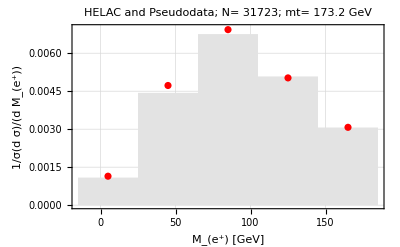

```mathematica
crossectionhel={1067.00,1040.40,1067.18,985.914,960.451};
filehel=Table[FileNames[][[i]],{i,1,nmass}];

datahel=Block[{list},
list=Reap[Do[Sow[ReadList[filehel[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahisthel[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[datahel[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossectionhel=Table[Reap[Do[Sow[datahel[[j,1]]],{j,1,nmass,1}]][[2,1,j,2]],{j,1,nmass}] (*fb*)

binshel=Partition[Block[{bin},
bin=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidthel=Table[(Max[binshel[[i]]]-Min[binshel[[i]]])/(nbins-1),{i,1,5}];
binsrealhel=Reap[Do[Sow[Chop[binshel[[i]]-binwidthel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrealhel[[i]],Max[binsrealhel[[i]]]+binwidthel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrealhel=Table[(Max[binsrealhel[[i]]]-Min[binsrealhel[[i]]])/(nbins),{i,1,nmass}];

valshel=Partition[Block[{val},
val=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnormhel=Table[valshel[[i]]/(crossectionhel[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

errorhel=Partition[Block[{err},
err=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnormhel=Table[errorhel[[i]]/(crossectionhel[[i]]),{i,1,nmass}];
normalisationhel=Round[Table[Sum[valsnormhel[[j,i]],{i,1,Length[valsnormhel[[j]]]}]*binwidthel[[j]],{j,1,nmass}]]

REBINNING HELAC;
valsnormrebinhel=Table[Table[Sum[Partition[valsnormhel[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
binsrebinhel=Table[Table[First[Partition[binshel[[j]],Round[nbins/rebin]][[i]]],{i,1,rebin}],{j,1,nmass}];
bwrebinhel=Table[(Max[binsrebinhel[[i]]]-Min[binsrebinhel[[i]]])/(rebin-1),{i,1,nmass}];
binsrebinrealhel=Reap[Do[Sow[Chop[binsrebinhel[[i]]-bwrebinhel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrebinrealhel[[i]],Max[binsrebinrealhel[[i]]]+bwrebinhel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrebinrealhel=Table[(Max[binsrebinrealhel[[i]]]-Min[binsrebinrealhel[[i]]])/(rebin),{i,1,nmass}];
errnormrebinhel=Table[Table[Sum[Partition[errnormhel[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
normalisationrebinhel=Round[Table[Sum[valsnormrebinhel[[j,i]],{i,1,Length[valsnormrebinhel[[j]]]}]*bwrebinrealhel[[j]],{j,1,nmass}]]


Which[int==1,
binhelac=binsrebin;
valhelac=valsnormrebin;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrebinreal;
errorhelac=errnormrebin;
,
int==2,
binhelac=binsrebinhel;
valhelac=valsnormrebinhel;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrebinrealhel;
errorhelac=errnormrebinhel;
]
valhelac
errorhelac
pseudoerror[stdnevents,3,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin]

histfromhelac[nmass_,bwreal_]:=Histogram[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]},PlotTheme->"Detailed",ChartBaseStyle->EdgeForm[None],ChartStyle->GrayLevel[0.89]]
histfromhelaclist[nmass_,bwreal_]:=HistogramList[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]}]

combine[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=Show[histfromhelac[nmass,bwreal],pseudoplot[nevents,3,binw,binsreal,bwreal,bins,nbins],
PlotTheme->"Detailed",
PlotLabel-> StringForm["HELAC and Pseudodata; N= ``; mt= `` GeV",nevents, mass[[nmass]]],
FrameLabel-> {StringForm["`` [GeV]",variable[[numbofdiffdist]]],StringForm["``",varnorm[[numbofdiffdist]]]}
]

pt1=combine[stdnevents,3,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,bwrebinreal,binsrebin,rebin]
```

```mathematica
THE  TOP MAS EXTRACTION PART;
```

```mathematica
FITTING THE VALUE OF DIFFERENTIAL VARIABLE FROM HELAC (THEORY) FOR EACH BIN FOR FIVE MASSES;
```

```mathematica
THEORETICAL VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormtheo=Reap[Do[Sow[valhelac[[All,i]]],{i,1,rebin,1}]][[2,1]]*(bwrebin[[1]]*rebin/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errorhelac[[All,i]]],{i,1,rebin,1}]][[2,1]]*(bwrebin[[1]]*rebin/npseudobin);

valsbindata[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},ErrorBar[errnormtheo[[int,i]]]}],{i,1,nmass,1}]][[2,1]]; (*for graph*)
valsbindatanozero[nbins_]:=Reap[Block[{valerr,nol},
valerr=Table[valsbindata[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},ErrorBar[0.]},{k,1,nmass}];
Sow[DeleteCases[valerr,nol]]]][[1]];

valsbintheo[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},errnormtheo[[int,i]]}],{i,1,nmass,1}]][[2,1]] (*{mass,vals},err*)
valsbintheonozero[nbins_]:=Reap[Block[{valerrtheo,nol},           (*{mass,vals},err NON ZERO BIN*)
valerrtheo=Table[valsbintheo[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},0.},{k,1,nmass}];
Sow[DeleteCases[valerrtheo, nol]]]][[1]];

valsbindatanozero[rebin];
valsbintheonozero[rebin];
```

```mathematica
NON ZERO BIN ENTRIES;
```

```mathematica
nonzerobin=If[MemberQ[Flatten[Transpose[valsnormtheo]],0.]==False,{"nothing"},
Block[{valstheo,errtheo,zero,nonzero,all,comp},
valstheo=Transpose[valsnormtheo];
errtheo=Transpose[errnormtheo];
zero=Reap[Do[If[valstheo[[i,j]]== 0 && errtheo[[i,j]]== 0,
Sow[{i,j}],Nothing],{i,1,nmass,1},{j,1,rebin,1}]
][[2]];
all=Flatten[Table[{Range[nmass][[i]],Range[rebin][[j]]},{i,1,nmass},{j,1,rebin}],1];
comp=Complement[all,zero[[1]]];
nonzero=If[zero≠ {},Reap[Sow[comp]],
Nothing]
][[1]]
]
```

{nothing}

```mathematica
FITTING FUNCTIONS;
```

```mathematica
value[nbins_]:=Reap[Do[Sow[valsbintheonozero[nbins][[i]][[All,1]]],{i,1,Length[valsbintheonozero[nbins]],1}]][[2,1]];
err[nbins_]:=Reap[Do[Sow[valsbintheonozero[nbins][[i]][[All,2]]],{i,1,Length[valsbintheonozero[nbins]],1}]][[2,1]];
fitting[nbins_]:=LinearModelFit[value[nbins][[#]],fitf,x,Weights->1/(err[nbins][[#]])^2]&/@ Range[1,Length[value[nbins]]];

value[rebin];
err[rebin];
fitting[rebin];
```

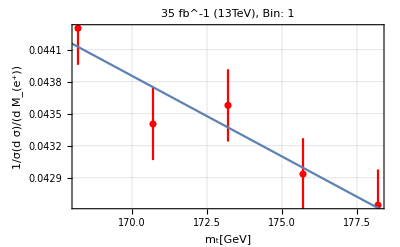
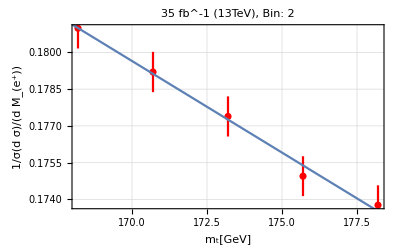
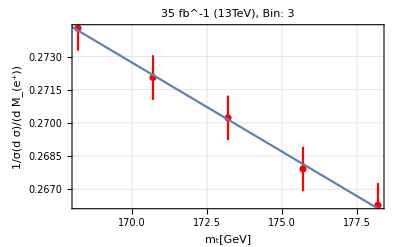
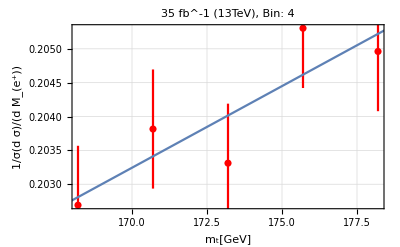
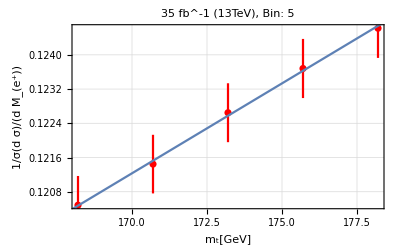

```mathematica
valsbinplot[int_,nbins_]:=ErrorListPlot[valsbindatanozero[nbins][[int]],PlotTheme->"Detailed",PlotLabel-> StringForm["`` fb^-1 (13TeV), Bin: ``",luminosity,int],PlotStyle->Red]
funcfit[int_,nbins_]:=Normal[fitting[nbins][[int]]]
funcbin[int_,nmass_,nbins_]:=funcfit[int,nbins]/.x-> mass[[nmass]]
combbinfunc[int_,nbins_]:=Block[{func},
func=funcfit[int,nbins]; (*fitting with polynomial arbitrary order*)
Show[valsbinplot[int,nbins],Plot[func,{x,160,180}],FrameLabel->{"m_t[GeV]",StringForm["``",varnorm[[numbofdiffdist]]]}]
]
allfit[nbins_]:=Table[combbinfunc[i,nbins],{i,1,Length[value[nbins]]}]

allfit[rebin]
```

```mathematica
PSEUDODATA VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
fact=(bwrebin[[1]]*rebin/npseudobin);

valsnormpseudo[nevents_,binw_,binsreal_,bins_,nbins_]:=Block[{valspseudo},
valspseudo=Reap[Do[Sow[pseudopointy[nevents,i,binw,binsreal,bins]*fact],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,valspseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[valspseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value[nbins]]] (*length value=non zero bins total*)
]
]
]
errnormpseudo[nevents_,binw_,binsreal_,bins_,nbins_]:=Block[{errpseudo},
errpseudo=Reap[Do[Sow[pseudoerror[nevents,i,binw,binsreal,bins,nbins]*fact],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,errpseudo,
MemberQ[nonzerobin,Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[errpseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value[nbins]]]
]
]
]

PSDATA USD FORG THE CHISQUARE;

valuep1=valsnormpseudo[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin][[number]];
errorp1=errnormpseudo[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin][[number]];
zeropost=Position[errorp1,0.]; 
errorp=Delete[errorp1,zeropost];
valuep=Delete[valuep1,zeropost];
(*pseudo data used only using the 173.2 GeV and dynamical Scale as the best theoretical prediction*)

valuep
errorp
```

{0.0466464,0.186059,0.277955,0.207221,0.118145}

{0.00107536,0.00195384,0.00220975,0.00201356,0.00164736}

```mathematica
THE χ^2 PROCEDURE;
```

162.831

{159.736,165.926}

3.09486

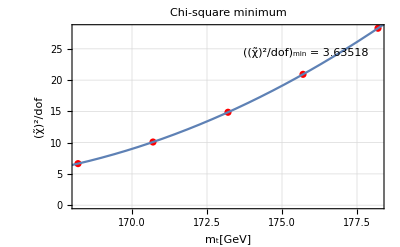

162.831±3.09486

```mathematica
CHI SQUARE STUFF;

chisquarebin[pvalue_,perror_,int_,mass_,nbins_]:=N[(pvalue[[int]]-fitting[nbins][[int]][mass])^2/(perror[[int]]^2)];
sumchisquare[pvalue_,perror_,mass_,nbins_]:=N[Sum[chisquarebin[pvalue,perror,i,mass,nbins],{i,1,Length[pvalue]-1}]];
chitilde[pvalue_,perror_,mass_,nbins_]:=N[sumchisquare[pvalue,perror,mass,nbins]/(Length[pvalue]-2)]
minchitilde[pvalue_,perror_,nbins_]:=x/.Last[FindMinimum[chitilde[pvalue,perror,x,nbins],{x,168.2,178.2}]]


chidata=ParallelTable[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]],rebin],{i,1,nmass}][[j]]},{j,1,nmass}];
minimumx=minchitilde[valuep,errorp,rebin];
minchi=chitilde[valuep,errorp,minimumx,rebin];
chivaluebnd=minchi+1;
chifunc=LinearModelFit[chidata,{1,x,x^2},x];
minimumx

deltamassbnd=x/.Solve[Normal[chifunc]==chivaluebnd,x] (*finding the corresponding m value for given chi square value without divide by dof*)
deltam1=Mean[Abs[minimumx-deltamassbnd]]

chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifunc],{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["((χ̃)^2/dof)_min = " <> ToString[minchi]],Background->White],Scaled[{.75,.85}]]]
PlusMinus[minimumx,deltam1]
```

```mathematica
BEFORE DIVIDED BY DEGREE OF FREEDOMS (EXTRACTING ONE DELTA MASS);
```

{{168.2,19.9336},{170.7,30.299},{173.2,44.5796},{175.7,62.7753},{178.2,84.8862}}

11.9055

{161.044,164.618}

{1.78682,-1.78682}

1.78682

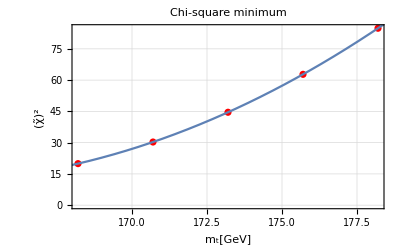

162.831±1.78682

```mathematica
minchitilderaw[pvalue_,perror_,nbins_]:=x/.Last[FindMinimum[sumchisquare[pvalue,perror,x,nbins],{x,168.2,178.2}]]

chidataraw=ParallelTable[{mass[[j]],Table[sumchisquare[valuep,errorp,mass[[i]],rebin],{i,1,nmass}][[j]]},{j,1,nmass}];
mmiddle=minchitilderaw[valuep,errorp,rebin];
minchiraw=sumchisquare[valuep,errorp,mmiddle,rebin];
chivaluebound=minchiraw+1;
chidataraw
chivaluebound
chifuncraw=LinearModelFit[chidataraw,{1,x,x^2},x];
deltamassbound=x/.Solve[Normal[chifuncraw]==chivaluebound,x] (*finding the corresponding m value for given chi square value without divide by dof*)
mmiddle-deltamassbound
deltamone=Mean[Abs[mmiddle-deltamassbound]]


chiparabolaraw=Show[ListPlot[chidataraw,FrameLabel-> {"m_t[GeV]","(χ̃)^2"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifuncraw],{x,160,180}],PlotLabel->"Chi-square minimum"]
PlusMinus[mmiddle,deltamone]
```

```mathematica
FITTED MASS ;
```

{157.431,157.928,159.493,163.518,168.551}

{1.80749,1.80734,1.79219,1.78012,1.76641}

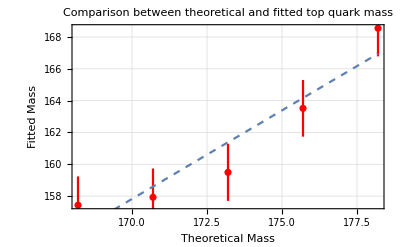

```mathematica
fittingmass[nevents_,binw_,binsreal_,bins_,nbins_,m_]:=Reap[
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,result,chisqraw,datachiraw,fchiraw,chibound,deltambound,deltameins},
pvaluelist=valsnormpseudo[nevents,binw,binsreal,bins,nbins][[m]];
perrorlist=errnormpseudo[nevents,binw,binsreal,bins,nbins][[m]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
chisqraw=ParallelTable[sumchisquare[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
datachiraw=ParallelTable[{mass[[j]],chisqraw[[j]]},{j,1,nmass}];
fchiraw=LinearModelFit[datachiraw,{1,x,x^2},x];
mout=minchitilderaw[pvaluelist,perrorlist,nbins];
chibound=sumchisquare[pvaluelist,perrorlist,minchitilderaw[pvaluelist,perrorlist,nbins],nbins]+1;
deltambound=x/.Solve[Normal[fchiraw]==chibound,x];
deltameins=Mean[Abs[mout-deltambound]];
result=Sow[{mout,deltameins}]
]
][[2,1]];

massfit=Reap[Do[Sow[fittingmass[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin,i]],{i,1,nmass,1}]][[2,1]];
masschi=Reap[Do[Sow[Flatten[massfit[[i]],1]],{i,1,nmass,1}]][[2,1]];
fitmass=masschi[[All,1]]
fitmasserr=masschi[[All,2]]

PLOTTING THE THEORETICAL MASS AND THE MASS FROM CHI SQUARE + 1 ANALYSIS  FROM ONE PSEUDO EXPERIMENTS(NO BIASED);
fitmassplot=ErrorListPlot[Table[{{mass[[i]],fitmass[[i]]},ErrorBar[fitmasserr[[i]]]},{i,1,nmass}],PlotTheme->"Detailed",PlotStyle->Red];
fitmassfunc=Fit[Table[{mass[[i]],fitmass[[i]]},{i,1,nmass}],{1,x},x];
fittmass=Show[fitmassplot,Plot[fitmassfunc,{x,168.2,178.2},PlotStyle->Dashed],PlotTheme->"Detailed",FrameLabel-> { "Theoretical Mass","Fitted Mass"},PlotLabel-> "Comparison between theoretical and fitted top quark mass"]
```

```mathematica
N -PSEUDO EXPERIMENTS;
```

```mathematica
npseudoexp[nevents_,binw_,binsreal_,bins_,nbins_,n_]:=Partition[Reap[
For[k=1,k<n+1,k++,
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,chisqmin,result,pvalue},
pvaluelist=valsnormpseudo[nevents,binw,binsreal,bins,nbins][[number]];
perrorlist=errnormpseudo[nevents,binw,binsreal,bins,nbins][[number]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
mout=minchitilderaw[pvaluelist,perrorlist,nbins];
chisqmin=chitilde[pvaluelist,perrorlist,mout,nbins];
pvalue=ChiSquarePValue[chisqmin*(Length[pvaluelist]-2),(Length[pvaluelist]-2)][[2]];
result=Sow[{mout,chisqmin,pvalue}]
]
];
][[2,1]],n];

exp=Reap[Sow[npseudoexp[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin,npseudo]]][[2,1,1,1]];
```

```mathematica
SOME STATISTICS AND  HISTOGRAMS ABOUT PSEUDO EXPERIMENT;
```

{0.187084,0.328036,0.359029,0.492425,0.625189,0.650752,0.713263,0.743214,0.754728,0.75883,0.773869,0.866022,0.946374,1.05761,1.10138,1.18422,1.22433,1.24033,1.33995,1.35704,1.36929,1.48652,1.49151,1.52149,1.52491,1.54297,1.55125,1.55735,1.63349,1.68632,1.72629,1.74457,1.79627,1.85315,1.89428,1.89685,1.89731,1.89849,1.9532,1.97368,1.97741,1.9825,2.02943,2.04987,2.15305,2.15493,2.16665,2.20643,2.22068,2.24401,2.31965,2.33847,2.35029,2.36284,2.38114,2.4058,2.41647,2.45659,2.57855,2.60429,2.63646,2.64756,2.72767,2.74498,2.78417,2.78794,2.84652,2.85697,2.91577,2.9205,2.92452,2.92617,2.97399,3.12878,3.19202,3.22136,3.24903,3.25642,3.28833,3.3442,3.64693,3.72022,3.77946,3.79788,3.82844,4.04728,4.0784,4.08998,4.3008,4.33418,4.53642,4.74953,4.87994,5.46806,5.68091,6.35521,6.39739,6.42208,6.9151,7.10087}

{{160.066,0.187084},{159.541,0.328036},{158.451,0.359029},{156.895,0.492425},{160.611,0.625189},{160.109,0.650752},{159.427,0.713263},{162.295,0.743214},{157.536,0.754728},{160.141,0.75883},{159.974,0.773869},{159.588,0.866022},{160.42,0.946374},{161.726,1.05761},{158.679,1.10138},{160.311,1.18422},{160.866,1.22433},{162.885,1.24033},{158.641,1.33995},{159.56,1.35704},{160.992,1.36929},{159.794,1.48652},{162.392,1.49151},{159.72,1.52149},{161.256,1.52491},{159.512,1.54297},{161.964,1.55125},{159.729,1.55735},{162.336,1.63349},{161.198,1.68632},{159.81,1.72629},{163.381,1.74457},{162.067,1.79627},{160.252,1.85315},{160.104,1.89428},{160.319,1.89685},{160.896,1.89731},{160.91,1.89849},{161.401,1.9532},{159.692,1.97368},{162.213,1.97741},{162.075,1.9825},{158.746,2.02943},{161.588,2.04987},{159.571,2.15305},{160.526,2.15493},{163.596,2.16665},{159.332,2.20643},{160.706,2.22068},{157.917,2.24401},{161.837,2.31965},{161.663,2.33847},{160.437,2.35029},{162.847,2.36284},{160.737,2.38114},{159.728,2.4058},{161.93,2.41647},{162.822,2.45659},{160.241,2.57855},{159.505,2.60429},{162.473,2.63646},{160.452,2.64756},{158.053,2.72767},{158.797,2.74498},{161.876,2.78417},{163.568,2.78794},{163.363,2.84652},{156.774,2.85697},{162.552,2.91577},{160.181,2.9205},{161.759,2.92452},{157.675,2.92617},{161.805,2.97399},{163.286,3.12878},{159.964,3.19202},{160.408,3.22136},{160.165,3.24903},{160.154,3.25642},{163.257,3.28833},{160.942,3.3442},{161.468,3.64693},{162.187,3.72022},{162.138,3.77946},{160.975,3.79788},{162.387,3.82844},{163.951,4.04728},{158.525,4.0784},{164.359,4.08998},{161.987,4.3008},{163.357,4.33418},{163.257,4.53642},{162.531,4.74953},{163.858,4.87994},{163.912,5.46806},{160.162,5.68091},{163.133,6.35521},{164.378,6.39739},{160.89,6.42208},{163.785,6.9151},{160.496,7.10087}}

100

2.53604

-Graphics-

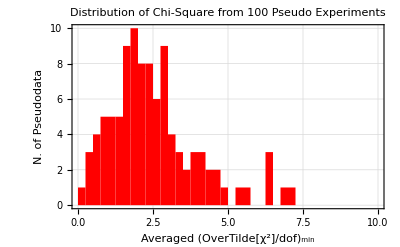

0.0548443

OneSidedPValue→0.176491

OneSidedPValue→0.187431

True

Theory, LO QCD | Variable | Luminosity [fb^-1] | m_t±δm_t[GeV] | Averaged ((χ̃)^2/dof)_min | Probability p-value | m_t^in-m_t^out [GeV]
Full, μ_0=mt | M_(e^+) | 35 | 160.987±1.55998 | 2.53604 | 0.0548443 (1.92011σ) | 12.2129

```mathematica
(*pexpmass=Delete[Sort[exp[[All,1]]],Partition[(-1)*Range[4*npseudo/100],1]]; (*96 percent of the mass data *)
pexpchisq=Delete[Sort[exp[[All,2]]],Partition[(-1)*Range[4*npseudo/100],1]] (*96 percent of the chi square min data due to isolated big value of chi*)
*)

pexpchisq=Sort[exp[[All,2]]]

ELIMINATE THI  CHI-SQUARE THAT IS MORE THAN CHI SQUARE STANDARD FOR ET2;
chistandard=50;
newexp=Reap[Do[
Which[scalename[[k]]=="et2",
If[(pexpchisq[[i]]<chistandard)&&(pexpchisq[[i]]==exp[[j,2]]),Sow[{exp[[j,1]],exp[[j,2]]}],Nothing],
scalename[[k]]=="mt",
Nothing],
{k,1,Length[scalename],1},{i,1,Length[pexpchisq],1},{j,1,Length[exp],1}]][[2,1]]
Length[newexp]
pexpmass=newexp[[All,1]];
pexpchis=newexp[[All,2]];

massout=Mean[pexpmass];

deltamassout=Reap[Block[{sortedmass,variance},
sortedmass=pexpmass;
variance=Sort[Reap[Do[Sow[Abs[sortedmass[[i]]-Mean[sortedmass]]],{i,1,Length[sortedmass],1}]][[2,1]]]; (*sorted the spread of the data from the mean*)
Sow[variance[[Round[68*Length[sortedmass]/100]]]] (*take the 68% CL i.e take the 68%*Number-th of the data as the error*)
]][[2,1,1]];

chiout=Mean[pexpchis]

pexpmasshist=Histogram[pexpmass,{168,178,0.25},PlotTheme->"Detailed",FrameLabel->{"Averaged m_t [GeV]","N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red, PlotLabel-> "Distribution of the top quark mass from " <>ToString[Length[pexpchis]] " Pseudo Experiments"]
pexpchisqhist=Histogram[pexpchis,{0,10,0.25},PlotTheme->"Detailed",FrameLabel-> {"Averaged (OverTilde[χ^2]/dof)_min", "N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red,PlotLabel-> "Distribution of Chi-Square from " <>ToString[Length[pexpchis]]<>" Pseudo Experiments"]

SOME RESULTS;

pvalue[pvalue_]:= ChiSquarePValue[chiout*(Length[pvalue]-2),Length[pvalue]-2][[2]];
pvout=pvalue[valuep]
nraw:=Sqrt[2]InverseErf[1-pvout]
ChiSquarePValue[1.58*4,4]
ChiSquarePValue[0.71*19,19]
Sort[exp[[All,3]]];
(*pvout=Mean[Sort[exp[[All,3]]]]*)
pvout>pvaluestandard
(*stddeviations=(Abs[massout[[number]]]*Sqrt[Length[pexpmass]/2])/InverseErfc[pvout]*10^-3*)
deltam=mass[[number]]-massout;
result=Grid[{{"Theory, LO QCD", "Variable","Luminosity [fb^-1]",ToString[PlusMinus[Subscript[m, t],Subscript[δm, t]],StandardForm]<>"[GeV]", "Averaged ((χ̃)^2/dof)_min","Probability p-value","m_t^in-m_t^out [GeV]"},
{StringForm["Full, μ_0=``",scale[[int]]],variable[[numbofdiffdist]],luminosity,PlusMinus[N[massout,2],N[deltamassout,2]],chiout,pvout "("<>ToString[N[nraw]]<> "σ)",deltam}},Frame->All]
```

```mathematica
EXPORTING FIGURES;
```

```mathematica
(*
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudodata"<>".pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudo_vs_theo_each_bin.pdf",allfit[rebin]];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_parabola_chi_square.pdf",chiparabola];*)
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_mass fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_result_table.pdf", result];*)
```

```mathematica
(*If[luminosity==5,
Do[
Export["kdata_"<>ToString[varname[[numbofdiffdist]]]<>"_"<>ToString[rebin]<>"_"<>massname[[i]]<>"_"<>scalename[[int]]<>".txt",Transpose[{binsrebin[[i]],valhelac[[i]]}],"Table"],
{i,1,nmass,1}
],
Nothing
]
```